## Problem 8

```mathematica
Subscript[s, 1]=DSolve[{y'[t]==t Exp[3t]-2y[t],y[0]==0},y,{t,0,1}]
```

{{y→Function[{t},1/25 ⅇ^(-2 t) (1+ⅇ^(5 t) (-1+5 t))]}}

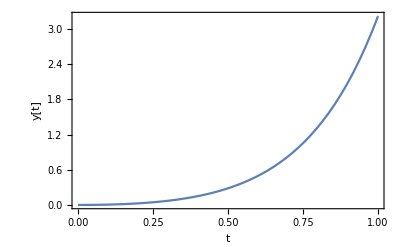

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 1]],{x,0,1},Frame->True,FrameLabel->{"t","y[t]"}]
```

```mathematica
Subscript[s, 2]=DSolve[{y'[t]==1-(t-y[t])^2,y[2]==1},y,{t,2,3}]
```

{{y→Function[{t},(1-3 t+t^2)/(-3+t)]}}

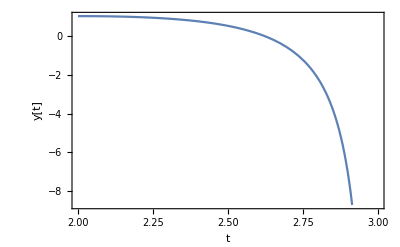

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 2]],{x,2,3},Frame->True,FrameLabel->{"t","y[t]"}]
```

```mathematica
Subscript[s, 3]=DSolve[{y'[t]==1+y[t]/t,y[1]==2},y,{t,1,2}]
```

{{y→Function[{t},t (2+Log[t])]}}

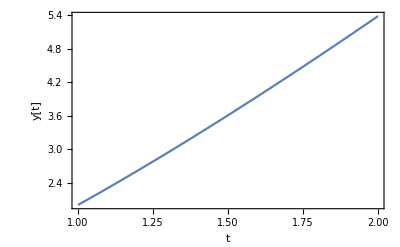

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 3]],{x,1,2},Frame->True,FrameLabel->{"t","y[t]"}]
```

```mathematica
Subscript[s, 4]=DSolve[{y'[t]== Cos[2t]+Sin[3t],y[0]==1},y,{t,0,1}]
```

{{y→Function[{t},1/6 (8-2 Cos[3 t]+3 Sin[2 t])]}}

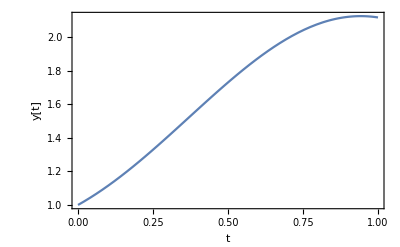

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 4]],{x,0,1},Frame->True,FrameLabel->{"t","y[t]"}]
```

## Problem 9

```mathematica
Subscript[s, 5]=NDSolve[{y''[x]==-Exp[-2 y[x]],y[1]==0,y[2]==Log[2]},y,{x,1,2}]
```

{{y→InterpolatingFunction[…]}}

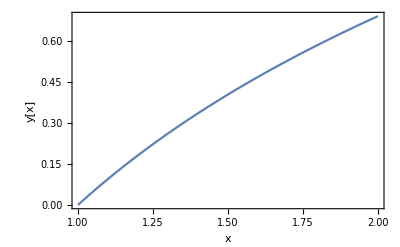

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 5]],{x,1,2},Frame->True,FrameLabel->{"x","y[x]"}]
```

```mathematica
Subscript[s, 6]=NDSolve[{y''[x]==y'[x]Cos[x]-y[x]Log[y[x]],y[0]==1,y[π/2]==ⅇ},y,{x,0,π/2}]
```

{{y→InterpolatingFunction[…]}}

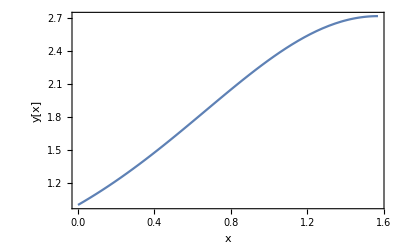

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 6]],{x,0,π/2},Frame->True,FrameLabel->{"x","y[x]"}]
```

```mathematica
Subscript[s, 7]=NDSolve[{y''[x]==-(2(y'[x])^3+(y[x])^2 y'[x])Sec[x],y[π/4]==2^(-1/4),y[π/3]==12^(1/4)/2},y,{x,π/4,π/3}]
```

{{y→InterpolatingFunction[…]}}

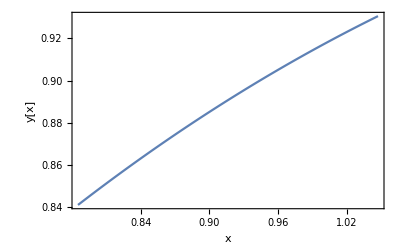

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 7]],{x,π/4,π/3},Frame->True,FrameLabel->{"x","y[x]"}]
```

```mathematica
Subscript[s, 8]=NDSolve[{y''[x]==1/2-(y'[x])^2/2-y[x]Sin[x/2],y[0]==2,y[π]==2},y,{x,0,π}]
```

NDSolve::ndsz: At x == 2.91947, step size is effectively zero; singularity or stiff system suspected.

NDSolve[{y''[x]==1/2-Sin[x/2] y[x]-1/2 y'[x]^2,y[0]==2,y[π]==2},y,{x,0,π}]

```mathematica
Plot[Evaluate[y[x]/. Subscript[s, 8]],{x,0,π},Frame->True,FrameLabel->{"x","y[x]"}]
```

ReplaceAll::reps: {NDSolve[{y''[x]==1/2-Sin[Times[«2»]] y[x]-1/2 ((«1»)^(«1»)[«1»])^2,y[0]==2,y[π]==2},y,{x,0,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000641782 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{y''[0.0000641782]==1/2-0.0000320891 y[0.0000641782]-1/2 ((«1»)^(«1»)[«1»])^2,y[0]==2,y[π]==2},y,{0.0000641782,0,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.0000641782 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{y''[0.0000641782]==0.5-0.0000320891 y[0.0000641782]-0.5 ((«1»)^(«1»)[«1»])^2,y[0.]==2.,y[3.14159]==2.},y,{0.0000641782,0.,3.14159}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::dsvar: 0.0641783 cannot be used as a variable.

General::stop: Further output of NDSolve::dsvar will be suppressed during this calculation.

-Graphics-